```mathematica
ClearAll["Global`*"]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/elastic_obstacle/monolithic/solution/data.csv"]
```

```mathematica
t = Table[ToExpression[{t[[i,1]],t[[i,6]]}],{i,2,Length[t]}]
```

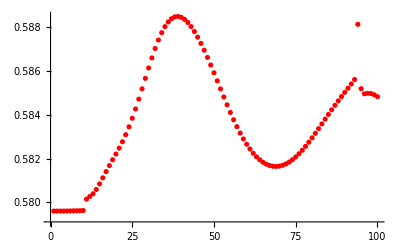

```mathematica
ListPlot[t,PlotStyle->Red]
```